# Уравнения математической физики

## Лектор: Корзюк Виктор Иванович, академик

## Преподаватель: Кулешов Александр Аркадьевич, аудитория 407

Студентка 9 группы 4 курса Харитонова Вероника Ренальдовна

# Решение линейных ДУ в частных производных 2-го порядка с двумя независимыми переменными и переменными коэффициентами.

В предыдущем ноутбуке замена независимых переменных, приводящих уравнение к каноническому виду, была найдена путем непосредственного решения уравнения характеристик функцией DSolve.

a22 (ω^(0,1)[x,y])^2+2 a12 ω^(0,1)[x,y] ω^(1,0)[x,y]+ a11 (ω^(1,0)[x,y])^2 = 0

В курсе уравнений математической физики методы решения нелинейных дифференциальных уравнений 1-го порядка обычно не изучают, поэтому студентам неизвестны алгоритмы решения уравнений характеристик, заложенные в ядре системы Mathematica.В курсе уравнений математической физики детально разработан метод решения только уравнения характеристик, основанный на так называемом методе характеристик. Изложим кратко конструкцию этго метода. Наряду с уравнением характеристик (1) рассмотрим следующее уравнение:

A11[x,y](ⅆy/ⅆx)^2-2A12[x,y]ⅆy/ⅆx+A22[x,y]=0

Это нелинейное обыкновенное ДУ 1-го порядка. Рассмотрим подробно структуру решения этого уравнения. Для этого уравнение (2) рассматривают как квадратное уравнение относительно неизвестной ⅆy/ⅆx. Решая его относительно этой неизвестной, находим:

ⅆy/ⅆx=(A12+√(A12^2=A11*A22))/A11

ⅆy/ⅆx=(A12-√(A12^2=A11*A22))/A11

Уравнения (3),(4) известны в курсе ОДУ как уравнения 1-го порядка, разрешенные относительно 1-й производной вида

ⅆy/ⅆx=f[x,y]

В теории ОДУ развивается полная теория интегрирования уравнения вида (5). Из этой теории следует, что уравнения (3),(4) имеют однопараметрическое семейство решений y1=y1[x,c1] и y2=y2[x,c2] соответственно.

Эти однопараметрические семейства решений уравнений (3),(4) называют характеристиками ДУ в частных производных

a11[x,y]∂_(x,x) U[x,y]+2a12[x,y]∂_(x,y) U[x,y]+a22[x,y]∂_(y,y) U[x,y] +a1[x,y]∂_x U[x,y]+a2[x,y]∂_y U[x,y]+a0[x,y]U[x,y]= f[x,y]

Из теории уравнений вида (5) относительно уравнений (3),(4) известно, что характеристики образуют семейство трансверсальных кривых, т.е. через каждую точку плоскости проходит одна и только одна кривая семейства y1 и одна и только одна кривая семейства y2. При этом кривые y1 и y2 пересекаются под ненулевым углом в каждой такой точке.

Методы интегрирования упавнения (5) хорошо развиты и основываются на понятии интеграла ОДУ.

Определение. Интегралом уравнения (5) называют любую функцию ψ[x,y] двух переменных такую, что

ψ[x,y[x,c]]=c

где y[x,c] однопараметрическое семейство решений уравнения (5).

Если известен интеграл ψ[x,y], то однопараметрическое семейство решений уравнения (5) можно найти, решая функциональное уравнение.

ψ[x,y]=c

Поэтому уравнение (5) решают с помощью интеграла. Как правило решаются уравнения с разделяющимися переменными. Преимущества системы Mathematica в том, что в ней заложены методы решения достаточно сложных уравнений вида (5). Полезность рассмотрения уравнения (2) определяется следующей теоремой:

Теорема. Любой интеграл уравнения (2) является решением уравнения характеристик, а любое решение уравнения характеристик является интегралом уравнения (2).

Из этой теоремы вытекает способ определения замены независимых переменных, приводящих уравнение к каноническому виду. А именно: находят интегралы уравнений (3),(4) - пусть это будут функции ϕ, ψ - а затем полагают ξ=ϕ[x,y], η=ψ[x,y] - искомая замена независимых переменных, приводящая уравнение к каноническому виду.

Рассмотрим уравнение: ⅆy/ⅆx=x*y.

Задача: изобразить графически однопараметрическое семейство решений этого уравнения.

```mathematica
DSolve[D[y[x], x]==x*y[x],y[x],x]
```

{{y[x]→ⅇ^(x^2/2) C[1]}}

Таким образом, однопараметрическое семейство решений имеет вид сⅇ^(x^2/2). Изображают графически:

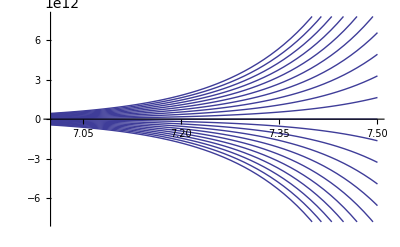

```mathematica
Plot[Table[c*Exp[x^2/2],{c,-10,10}],{x,7,7.5}]
```

Пример 2. Найдём семейство характеристик ДУ в частных производных в случае постоянных коэффициентов.

Решение. Главная часть такого уравнения может быть записана в виде

a(∂^2 u)/(∂x^2)+2b(∂^2 u)/(∂x∂y)+c(∂^2 u)/(∂y^2)+...= ...

В соответствии с приведением этого уравнения к каноническому виду, необходимо найти два интеграла следующих ОДУ:

(∂y)/(∂x)=(b+√(b^2-ac))/a

(∂y)/(∂x)=(b-√(b^2-ac))/a

Найдум 2 интеграла этих ОДУ.

```mathematica
ClearAll[y,x,a,b,c,α,ds1,ds2,y1,y2];
ds1=DSolve[D[y[x], x]==(b+√(b^2-a*c))/a,y[x],x]//Flatten
```

{y[x]→((b+√(b^2-a c)) x)/a+C[1]}

Находим однопараметрическое семейство решений 1-го ДУ

```mathematica
y1[x_,α_]=y[x]/.ds1/.C[1]->α
```

((b+√(b^2-a c)) x)/a+α

```mathematica
ds2=DSolve[D[y[x], x]==(b-√(b^2-a*c))/a,y[x],x]//Flatten
```

{y[x]→((b-√(b^2-a c)) x)/a+C[1]}

Находим однопараметрическое семейство решений 2-го ДУ

```mathematica
y2[x_,β_]=y[x]/.ds2/.C[1]->β
```

((b-√(b^2-a c)) x)/a+β

При конкретных значениях параметров a,b,c изобразим графически оба семейства характеристик на плоскости переменных x,y. Пусть

```mathematica
a=1;b=4;c=1;
```

```mathematica
tb1=Table[Plot[y1[x,α],{x,-10,10}, PlotRange->{{-10,10},{0,175}},DisplayFunction:>Identity], {α,0,100,5}];
```

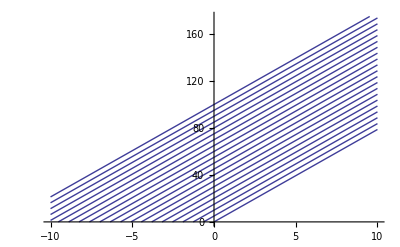

```mathematica
Show[tb1,DisplayFunction:>$DisplayFunction]
```

```mathematica
tb2=Table[Plot[y2[x,β],{x,-10,10}, PlotRange->{{-10,10},{0,175}},DisplayFunction:>Identity], {β,0,100,5}];
```

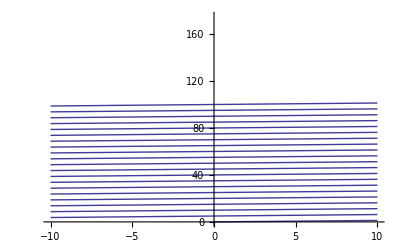

```mathematica
Show[tb2,DisplayFunction:>$DisplayFunction]
```

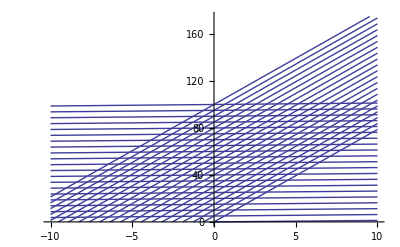

```mathematica
Show[tb1,tb2,DisplayFunction:>$DisplayFunction]
```